-Graphics-

# The Multiparadigm Data Science Workflow

## Data Wrangling

## Learning Objectives

Import real-world data from different sources

Data files

Databases

Curated data

External APIs

Web scraping

Convert raw data into computable format ready for analysis

Lists

Associations

Datasets

Entities

Time series

## Data Wrangling

Process of importing raw data and converting it into a suitable format for downstream analysis

Sometimes requires “hacking skills” to organize and clean messy data into an informative manageable dataset

Goal is to create code for semi-automated tools that would make the process easier the next time the workflow is used

## Importing Data from Files

Import data in various formats from existing data files on your local system.

### Formats Associated with Typical Data Files

Text and numeric data: .txt, .csv, .tsv, .xls, .xlsx

Images: .bmp, .jpeg, .png, .tiff, .svg

Structured web data: .html, .json, .xml

Archives: .zip, .gzip, .tar

Domain specific

Chemical & biomolecular formats: MOL, Affymetrix, AgilentMicroarray, FASTA, GenBank, ...

Geospatial formats: ArcGRID, GeoTIFF, GeoJSON, GPX, ...

Many others

### Formats Supported in the Wolfram Language

```mathematica
$ImportFormats
```

## Importing Data from Files

### Set Up

Set working directory:

```mathematica
SetDirectory[FileNameJoin[{NotebookDirectory[],"data"}]];
```

List the names of the files in a selected directory using FileNames:

```mathematica
FileNames[]
```

```mathematica
FileNames["*.csv"]
```

### Files Residing Locally on the System

Import data files from the local “data” directory.

Type in the filename (with complete path) or from menu Insert ▶ File Path ...:

```mathematica
stockdata =Import["stockdata.csv"];
```

```mathematica
citydata = Import["cities.xlsx"];
```

Take a peek at the data:

```mathematica
stockdata//Shallow
```

```mathematica
citydata //First
```

### Files Residing on the Web

Import files from the web directly using the URL:

```mathematica
financeData =Import["https://go.microsoft.com/fwlink/?LinkID=521962"];
```

```mathematica
financeData//Dimensions
```

### Check File Information before Actually Importing

Examine the elements that are available for import:

```mathematica
Import["https://go.microsoft.com/fwlink/?LinkID=521962","Elements"]
```

Import the element of interest:

```mathematica
financeData =Import["https://go.microsoft.com/fwlink/?LinkID=521962",{"Sheets",1}];
```

```mathematica
financeData//Dimensions
```

A summary of information about the file itself:

```mathematica
Import["stockdata.csv","Summary"]
```

### Saving and Importing Intermediate Results in the Wolfram Language

A useful approach to save mid-pipeline restructured data is to save Wolfram Language expressions in files using Save or DumpSave. The saved files can be read in again at a later session using Get:

```mathematica
financeData[[1;;10]]
```

```mathematica
financeDataSamples =RandomSample[Drop[financeData,5],100]
```

```mathematica
DumpSave["financeDataSamples.mx",financeDataSamples]
```

```mathematica
Clear[financeDataSamples]
```

```mathematica
FindFile["financeDataSamples.mx"]
```

```mathematica
<<"financeDataSamples.mx"
```

## Importing Data from a Database

### Set Up

DatabaseLink contains a number of example databases. Install them as follows:

```mathematica
<<DatabaseLink`DatabaseExamples`;
DatabaseExamplesBuild[]
```

### Connecting to an SQL Database

Load the DatabaseLink package:

```mathematica
Needs["DatabaseLink`"];
```

Open a connection to the database (the “publisher” example database):

```mathematica
conn=OpenSQLConnection["publisher"]
```

### Getting Information from the Database

Check the names of the tables in the database:

```mathematica
SQLTableNames[conn]
```

#### Using Wolfram Language functionality to select rows of data from a table

Select a few rows from the “SALESDETAILS” table showing the column headers:

```mathematica
SQLSelect[conn,"SALESDETAILS","ShowColumnHeadings"-> True,"MaxRows"-> 5]
```

Select the titles as well as quantity ordered in each sales order (final goal is to compute the total quantity ordered for each title):

```mathematica
data =SQLSelect[conn,"SALESDETAILS",{"TITLE_ID","QTY_ORDERED"}]
```

Use Wolfram Language code to group the sales orders by title and sum the quantities across orders for each title:

```mathematica
data2 ={First@#[[All,1]],Total[#[[All,2]]]}&/@GatherBy[data,First]
```

Visualise the total sales for each title:

```mathematica
BarChart[data2[[All,2]],ChartLabels->Placed[data2[[All,1]],Below,Rotate[#,Pi/2]&]]
```

#### Using SQL to select rows of data from a table

Use SQL directly to group results by title and add up the quantity ordered in each group:

```mathematica
data3 =SQLExecute[conn,"Select TITLE_ID, SUM(QTY_ORDERED) from SALESDETAILS group by TITLE_ID"]
```

Create a pie chart to show total sales for the titles:

```mathematica
PieChart[data3[[All,2]],ChartLabels->Placed[data3[[All,1]],"RadialCallout"]]
```

### Housekeeping

Check for open connections:

```mathematica
SQLConnections[]
```

Close connections that you do not need:

```mathematica
CloseSQLConnection[conn]
```

## Accessing Built-in Data: Wolfram Knowledgebase

### Types of Built-in Data

The Wolfram Language provides a built-in collection of high-quality curated datasets spanning a variety of topics.

Physics and Chemistry Data

Earth Sciences Data

Engineering Data, Transportation Data

Socioeconomic & Demographic Data

Life Sciences& Medicine Data

List the names of types of example data:

```mathematica
ExampleData[]
```

List of the elements or properties available for a particular example:

```mathematica
ExampleData[{"Text","USConstitution"},"Properties"]
```

List some of the different types of data collections:

```mathematica
RandomSample[Names["*Data"],10]
```

For a complete listing:

```mathematica
Names["*Data"]
```

## Accessing Built-in Data: Wolfram Data Framework

The Wolfram Data Framework makes use of the Wolfram Language and the Wolfram Knowledgebase to provide a way for users to access the curated data.

### Entity

Tight integration of data from the Wolfram Knowledgebase with the Wolfram Language

200+ entity types accessible through natural language input or direct programmatic access

An Entity is a canonical object representing some real-world data:

```mathematica
LinguisticAssistant
```

```mathematica
LinguisticAssistant
```

A list of currently available entity types is given by:

```mathematica
EntityValue[]
```

```mathematica
RandomSample[EntityValue[],25]
```

A list of sample entities belonging to a particular class of entities can be viewed with:

```mathematica
EntityValue["Person","SampleEntities"]
```

The available properties of an Entity can be viewed with:

```mathematica
EntityValue["Person","Properties"]
```

```mathematica
EntityValue[Entity["Person","JKRowling::z8f97"],"Dataset"]
```

Entity values can be accessed through natural language input:

```mathematica
LinguisticAssistant
```

TimeSeries[…]

A hybrid approach with natural language input and programming language keyword:

```mathematica
LinguisticAssistant["TaxonomyGraph"]
```

### Interpreter

At least as many Interpreters as entities in the Wolfram language:

```mathematica
$InterpreterTypes
```

A string can be converted into an entity in the Wolfram Language to augment your data:

```mathematica
Interpreter["City"]["Champaign"]
```

An entity immediately provides access to a lot more information:

```mathematica
Entity["City",{"Champaign","Illinois","UnitedStates"}]["Properties"]
```

## Accessing Built-in Data: Wolfram Data Repository

A public resource for computable datasets, curated and structured for immediate use—computation, visualisation or analysis: https://datarepository.wolframcloud.com

### Searching for Data

Searching for data programmatically with the Wolfram Language:

```mathematica
ResourceSearch["Statistics",5]
```

Browsing or searching on the website:

### Getting the Data

To import the data on Meteorite Landings (a collection of known meteorite landings) from the Data Repository:

```mathematica
meteoriteData = ResourceData["Meteorite Landings"]
```

Dataset[<>]

### Working with the Data

Find the most common classes of meteorites:

```mathematica
meteoriteData[Counts /* ReverseSort,"Classification"]
```

A visual representation of the same information:

```mathematica
meteoriteData[WordCloud,"Classification"]
```

A geographic visualisation of the landing sites of 500 random samples indicating the size of the sample:

```mathematica
GeoBubbleChart[RandomSample[meteoriteData,500][All,#Coordinates->#Mass&]]
```

## Getting Data from Web APIs

Sometimes you want to import data offered through the API of an online service like Twitter, LinkedIn, Facebook, etc.

### Connect to Twitter

```mathematica
$Services
```

{ArXiv,AWS,BingSearch,CharityEngine,ChemSpider,CrossRef,Dropbox,Facebook,Factual,FederalReserveEconomicData,Fitbit,Flickr,GoogleAnalytics,GoogleCalendar,GoogleContacts,GoogleCustomSearch,GooglePlus,GoogleTranslate,Instagram,IPFS,LinkedIn,MailChimp,MicrosoftTranslator,Mixpanel,MusicBrainz,OpenLibrary,OpenPHACTS,PubChem,PubMed,Pushbullet,Reddit,RunKeeper,SeatGeek,SurveyMonkey,Twilio,Twitter,Wikipedia,Yelp}

```mathematica
tw=ServiceConnect["Twitter","New"]
```

ServiceObject[…]

When signing in for the first time:

-Graphics-
     -Graphics-
     ServiceObject[…]

If already signed in from a browser:

```mathematica
tw=ServiceConnect["Twitter", "New"];
```

-Graphics-

### Download Data from Twitter

Get a list of tweets by a particular user:

```mathematica
tw["TweetList","Username"->"WolframResearch",MaxItems->5]
```

Get a list of tweets with a particular hashtag:

```mathematica
tweets =tw["TweetSearch","Query"-> "#mathematics",MaxItems->10]
```

Extract just the text of the tweets:

```mathematica
tweets[All,"Text"]
```

Determine if the tweet is a positive or negative comment:

```mathematica
Classify["Sentiment",tweets[All,"Text"]]
```

### Housekeeping

Disconnect the service for housekeeping:

```mathematica
ServiceDisconnect[tw]
```

## Getting Data from the Web

### Searching the Web with Search Engines: Google or Bing

Generic web search:

```mathematica
WebSearch["Christopher Robin","Snippets"]
```

```mathematica
WebSearch["Christopher Robin","Hyperlinks",Method->"Google"]
```

### Searching for Images on the Web

Restricting search to images:

```mathematica
WebImageSearch["Christopher Robin"]
```

```mathematica
WebImageSearch["Christopher Robin","Images"]
```

### Searching for Data on Wikipedia

Restricting search to Wikipedia articles:

```mathematica
WikipediaSearch["Content"->"Christopher Robin",MaxItems->25]
```

### Importing Data from Wikipedia

Get the text from the Wikipedia article on Christopher Robin:

```mathematica
WikipediaData["Christopher Robin","SummaryPlaintext"]
```

Get a list of rules representing links from other articles into the article on Christopher Robin:

```mathematica
links=WikipediaData["Christopher Robin","BacklinksRules","MaxLevelItems"->20,"MaxLevel"->2];
```

Visualise the collection of articles as a graph:

```mathematica
Graph[links,VertexLabels->Placed["Name",Tooltip],VertexStyle->{"Christopher Robin"->Red}]
```

## Scraping Data off Webpages

### Import the Webpage

Get the entire webpage as a String:

```mathematica
wolframWebpage =Import["https://www.wolfram.com/language"]
```

Check the types of elements that can be imported from the webpage:

```mathematica
wolframWebpageHTML =Import["https://www.wolfram.com/language","Elements"]
```

### Import Images

Import only the images from the webpage:

```mathematica
wolframImages =Import["https://www.wolfram.com/language","Images"]
```

### Import Hyperlinks

Import only the hyperlinks on the webpage:

```mathematica
wolframLinkOuts =Import["https://reference.wolfram.com/language","Hyperlinks"]
```

### Exercise

Import the hyperlinks from the page “https://www.wolfram.com/language”.

Solution

Check the size of the imported data.

Solution

Remove duplicates and check the size of the dataset again.

Solution

Check a random sample from the dataset.

Solution

Use string pattern matching to get the domain and path from the URL of the random sample.

Solution

Group the data by domain name.

Solution

Identify the two domains that have the most links.

Solution

#### Complete solution

```mathematica
wolframPageLinks =Import["https://www.wolfram.com/language","Hyperlinks"]
```

```mathematica
wolframPageLinks //Length
```

```mathematica
wolframPageLinks//DeleteDuplicates//Length
```

```mathematica
RandomSample[wolframPageLinks,1]
```

```mathematica
StringSplit[RandomSample[wolframPageLinks,1],Repeated["/"]]
```

```mathematica
domains =GroupBy[Rest[StringSplit[#,Repeated["/"]]]&/@ DeleteDuplicates[wolframPageLinks],First]
```

```mathematica
ReverseSort[Length /@ domains]
```

## Useful Data Sources for Data Science Projects

Some sites for publicly available datasets:

US Government’s open data: https://www.data.gov

UCI Machine Learning Repository: https://archive.ics.uci.edu/ml/datasets.php

Kaggle Data Science Contests: https://www.kaggle.com/datasets

FiveThirtyEight blog: https://github.com/fivethirtyeight/data

Note: This list has only been compiled as a suggestion for resources. Wolfram Research, Inc. is unable to comment on the quality of the content there.

## Data Wrangling: From Raw Data into Lists

Lists are the most basic data structures in the Wolfram Language for easy manipulation of data.

### Getting the Data

Import the “RetailSales.tsv” data file:

```mathematica
rawData =Import["ExampleData/RetailSales.tsv","TSV"];
```

### Working with the Data

#### Basic list manipulations

Take a peek at the data—first few rows at the beginning of the list:

```mathematica
rawData //Shallow
```

Check how many rows and columns:

```mathematica
rawData //Dimensions
```

If there is a header row, extract it for labelling purposes later:

```mathematica
columnHeaders = First@rawData
```

{Date,City,Sales}

Extract the data without the header rows:

```mathematica
salesData = Rest@rawData
```

Extract specific columns of data:

```mathematica
salesByDate =salesData[[All,{1,3}]];
salesByCity =salesData[[All,{2,3}]];
```

#### Visualisations using lists

Gather sales data for each date, across cities:

```mathematica
GatherBy[salesByDate,First]
```

Total sales for each date:

```mathematica
{#[[1,1]],Total@#[[All,-1]]}&/@GatherBy[salesByDate,First]
```

Visualise daily total sales for the available months:

```mathematica
dailySalesData ={#[[1,1]],Total@#[[All,-1]]}&/@GatherBy[salesByDate,First];
DateListPlot[dailySalesData]
```

Gather sales data for each city:

```mathematica
GatherBy[salesByCity,First]
```

Total sales for each city:

```mathematica
{#[[1,1]],Total@#[[All,-1]]}&/@GatherBy[salesByCity,First]
```

Visualise total sales for each city for the available months:

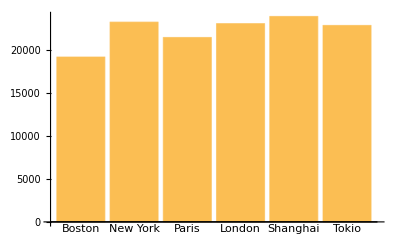

```mathematica
citySalesData =
{#[[1,1]],Total@#[[All,-1]]}&/@GatherBy[salesByCity,First];
BarChart[citySalesData[[All,-1]],ChartLabels->citySalesData[[All,1]]]
```

## Data Wrangling: From Raw Data to Key-Value Pairs

An Association represents data as key-value pairs.

Associations provide the dictionary data structure, where each value is labelled with and accessed by its key. This removes the need to remember separately the meaning of each entry in a list and strictly adhere to the sequence:

```mathematica
assoc=<|a->4,b->2,c->1,d->5|>
```

### Basic Operations

Look up a value by key:

```mathematica
assoc[b]
```

```mathematica
assoc[[2]]
```

```mathematica
assoc[[Key[b]]]
```

Many common list operations work transparently on associations:

```mathematica
Map[f,assoc]
```

```mathematica
Sort@assoc
```

```mathematica
Select[assoc,#>3&]
```

```mathematica
Total[assoc]
```

Some functions apply to keys:

```mathematica
KeyMap[f,assoc]
```

```mathematica
KeySort[assoc]
```

Extract keys or values from an association:

```mathematica
Keys[assoc]
```

```mathematica
Values[assoc]
```

Functions such as AssociationMap and AssociationThread can construct associations from lists:

```mathematica
AssociationMap[f,{a,b,c,d}]
```

```mathematica
AssociationThread[{a,b,c,d},{1,2,3,4}]
```

Associations are also returned by using functions like GroupBy, Counts, CountsBy, etc. to process data.

### Working with Associations

Total sales for each city (using GroupBy instead of GatherBy):

```mathematica
citySalesData =GroupBy[salesByCity,First->Last,Total]
```

Number of sales for each city:

```mathematica
Counts[salesByCity[[All,1]]]
```

Organize sales data by city:

```mathematica
GroupBy[salesData,#[[2]]&]
```

Restructure the data so that for each city, a list of date-value pairs is stored:

```mathematica
citySalesDataByDates =Sort[#[[All,{1,3}]]]& /@GroupBy[salesData,#[[2]]&]
```

Plot sales data across all available dates, only for Boston:

```mathematica
DateListPlot[citySalesDataByDates["Boston"]]
```

Create a stacked plot comparing sales across three cities for a few days:

```mathematica
StackedDateListPlot[citySalesDataByDates[#][[;;30]]&/@{"Boston","Shanghai","London"},PlotLegends->{"Boston","Shanghai","London"}]
```

## Data Wrangling: From Raw Data to Hierarchical Structured Datasets

A Dataset is a general way of representing a hierarchy of lists and associations, constructed from tabular data.

It provides a flexible framework for sophisticated data queries and manipulations on data, given a defined regular structure at arbitrary complexity:

```mathematica
d=Dataset[{
<|"a"->1,"b"->"x","c"->{1}|>,
<|"a"->2,"b"->"y","c"->{2,3}|>,
<|"a"->3,"b"->"z","c"->{3}|>,
<|"a"->4,"b"->"x","c"->{4,5}|>
}];
```

### Basic Operations

Extract rows:

```mathematica
d[2;;4]
```

Extract a row:

```mathematica
d[2]
```

Extract the raw contents of a row:

```mathematica
Normal[d[2]]
```

Extract an element from a particular column of a particular row:

```mathematica
d[2,"b"]
```

Extract all rows of a particular column:

```mathematica
d[All,"a"]
```

#### Filtering, sorting, ...

A Dataset can be queried using a function or composition of functions.

Perform operations on a single column:

```mathematica
d[Total,"a"]
```

```mathematica
d[Catenate,"c"]
```

```mathematica
d[Tally,"b"]
```

Sort by some criterion:

```mathematica
d[SortBy[Length[#c]&]]
```

Filter rows based on one of the columns:

```mathematica
d[Select[#a>2&]]
```

Filter rows and extract a column:

```mathematica
d[Select[#a>2&],"b"]
```

Delete duplicates:

```mathematica
d[DeleteDuplicatesBy[Key["b"]]]
```

#### Optional

Filter rows, then aggregate a column (/* is an abbreviation for RightComposition):

```mathematica
d[Select[#b=="x"&]/*Total,"a"]
```

5

This is equivalent:

```mathematica
d[Select[#b=="x"&]]
```

Dataset[<>]

```mathematica
d[Select[#b=="x"&]][Total,"a"]
```

5

Group rows by one column and then operate on a second column based on that grouping:

```mathematica
d[GroupBy[Key["b"]],Catenate,"c"]
```

Dataset[<>]

### Examples

Revisiting the sales data as a Dataset:

```mathematica
citySalesDS =Dataset[citySalesDataByDates]
```

Look at total sales for Boston:

```mathematica
citySalesDS["Boston"][Total,2]
```

Try SemanticImport, which uses machine learning and does a decent job of automatically converting many kinds of data:

```mathematica
semanticSalesData =SemanticImport["ExampleData/RetailSales.tsv"]
```

Look at total sales for each city:

```mathematica
semanticSalesData[GroupBy["City"],Total,"Sales"]
```

### Exercise

Get the “Planets” dataset from ExampleData. This is a hierarchical dataset consisting of properties of solar system bodies:

```mathematica
p=ExampleData[{"Dataset","Planets"}]
```

Look at the underlying structure of the data.

Solution

Extract the names of the planets from the dataset.

Solution

Get the mass of Earth.

Solution

Get the radius of each planet.

Solution

List the satellites for each planet.

Solution

Provide the total number of satellites for each planet.

Solution

#### Complete solution

```mathematica
p=ExampleData[{"Dataset","Planets"}]
```

```mathematica
Normal[p]
```

```mathematica
Keys[p]
```

```mathematica
p["Earth","Mass"]
```

```mathematica
p[All,"Radius"]
```

```mathematica
p[All,"Moons"]
```

```mathematica
p[All,"Moons",Keys]
```

```mathematica
p[All,"Moons",Length]
```

## Data Wrangling: From Raw Data to Rich Computable Entities

It can be very useful to make data computable as you are collecting it. The Wolfram Data Framework can be leveraged to add more information to raw data.

### Turning Strings into Entities

Strings can be converted into entities to link the data item to additional information available about it in the Wolfram Knowledgebase.

Convert the string representing a city name into a city entity using SemanticInterpretation or Interpreter:

```mathematica
SemanticInterpretation["Tokyo"]
```

```mathematica
Interpreter["City"]["Tokyo"]
```

Get its geographical coordinates:

```mathematica
Entity["City", {"Tokyo", "Tokyo", "Japan"}]["Coordinates"]
```

Revisit the association citySalesData:

```mathematica
citySalesData
```

Create entities out of each city name:

```mathematica
citySalesData2 =KeyMap[SemanticInterpretation,citySalesData]
```

Present the sales data for each city on a map of the world:

```mathematica
GeoRegionValuePlot[citySalesData2,GeoLabels->(Tooltip[#1,Row[{#2,":",#4}]]&), PlotMarkers->GeoMarker]
```

### Importing Raw Data as Entities into a Dataset

Sample data file:

```mathematica
Import["ExampleData/buildings.dat"]
```

```mathematica
First[%]
```

Use SemanticImport to get entities directly:

```mathematica
buildingData =SemanticImport["ExampleData/buildings.dat",<|"Rank"->"Integer","Name"->"Building","City"->"City","Country"->"Country","Year"->"ComputedDate","Stories"->"Integer","Height"->Restricted["Quantity", "Meters"]|>,HeaderLines->1]
```

## Data Wrangling: From Time-Ordered Raw Data to Time Series Objects

For data indexed in time order, it is helpful to preserve the essence of this special ordering property.

### TimeSeries: Series of Time-Value Pairs

Create a TimeSeries out of the citySalesDataByDates:

```mathematica
tsSalesData =TimeSeries /@ citySalesDataByDates
```

Visualise the sales data for each city for the first two weeks of February:

```mathematica
DateListPlot[TimeSeriesWindow[#,{{2014,2,1},{2014,2,14}}]&/@tsSalesData]
```

Visualise the sales data for Boston for the first quarter of 2014:

```mathematica
DateListPlot@TimeSeriesWindow[tsSalesData["Boston"],{{2014,1,1},{2014,3,31}}]
```

Fit a model to the time series data for the first three months of 2014:

```mathematica
tsm = TimeSeriesModelFit[TimeSeriesWindow[tsSalesData["Boston"],{{2014,1,1},{2014,3,31}}],"SARIMA"]
```

Use the model to predict the sales for April 2014 and compare with the actual sales data from April 2014:

```mathematica
tsf=TimeSeriesForecast[tsm,{10}]
```

```mathematica
DateListPlot[{TimeSeriesWindow[tsSalesData["Boston"],{{2014,4,1},{2014,4,10}}],tsf},PlotLegends->{"data","forecast"}]
```

### TemporalData: Collection of Time Series

Import the “stockhighlowclose.tsv” file (ToExpression is needed to convert from strings to Wolfram Language expressions):

```mathematica
stockhighlowclose =ToExpression@Import["stockhighlowclose.tsv","TSV"];
```

Check Dimensions to see how many time series are actually present in the data:

```mathematica
stockhighlowclose//Dimensions
```

```mathematica
td1=TemporalData[stockhighlowclose]
```

### Exercise

Examine the "Properties" and "PathLengths" of the TemporalData object stockhighlowclose.

Solution

Find the “high,” “low” and “close” prices for “Jul 14 2006”.

Solution

Create a DateListPlot of the data.

Solution

#### Complete solution

```mathematica
td1["Properties"]
```

```mathematica
td1["PathLengths"]
```

```mathematica
td1["SliceData",{"Jul 14 2006"}]
```

```mathematica
DateListPlot[stockhighlowclose]
```

```mathematica
DateListPlot[stockhighlowclose,Joined-> {False,False,True},Filling-> {1-> {2}}]
```

## Summary

This section presented functionality to load data into the Wolfram Language and prepare it for further analysis.

Data can be imported

from local files, from the web and from databases

from the built-in knowledgebase and Wolfram Data Repository

by scraping content off webpages

Raw data needs to be converted into a structural and computable format useful for analysis.

Constructs available in the Wolfram Language for data storage and manipulation:

Lists

Associations

Datasets

Time series

Raw data can be enriched semantically by leveraging the Wolfram Data Framework to get additional information with the help of:

SemanticImport

SemanticInterpretation

Entities

## References

Importing and Exporting

For more details on working with numerical and textual data, refer to Loading Numerical Data Overview and Reading Textual Data.

Developing an Import Converter

Detailed instructions for working with SQL databases in the Wolfram Language and many different examples of connecting to databases and fetching data with both Wolfram Language-style queries and SQL queries can be found in the DatabaseLink User Guide.

More functions for accessing the continuously updated Wolfram Knowledgebase can be found in this tutorial on Knowledge Representation and Access.

The Wolfram Language offers functionality to get data from Flickr, SurveyMonkey, Fitbit, Runkeeper, PubMed, ArXiv, PubChem, etc. Here is a complete Listing of Supported External Services in the Wolfram Language.

The Wolfram Language contains numerous functions to transform and work with lists. For further details, please see these tutorials on Lists and Manipulating Lists. A number of functions to restructure and reorganize lists can be found at Rearranging & Restructuring Lists.

For more details on working with associations and datasets in the Wolfram Language, refer to these guides on Associations and Computation with Structured Datasets.

A Primer on Association and Datasets by Seth Chandler.

For more details on working with time series in the Wolfram Language, refer to Time Series.

Use Data from the Wolfram Data Repository

Curating Data and Integrating the Wolfram Data Framework—video course on Wolfram U